```mathematica
(* 
 Ahmed Qureshi
404335525
ahmed.qureshi@ucla.edu
HW 3
*)
```

```mathematica
(*1*)
Remove["Global`*"]
y[A_,k_,dir_,x_,t_]:=A*Sin[k*(x-dir*v*t)]
yr[A1_,k1_,dir1_,A2_,k2_,dir2_,x_,t_]:= y[A1,k1,dir1,x,t]+y[A2,k2,dir2,x,t];

A=1;
v=1;
k1=2π;
k2=k1+δk;
δk=0.75*π;

y1[A1_,k1_,dir1_,t_]:=Plot[y[A1,k1,dir1,x,t],{x,0,4},PlotStyle->Red];
y2[A2_,k2_,dir2_,t_]:=Plot[4+y[A2,k2,dir2,x,t],{x,0,4},PlotStyle->Blue];
yresultant[A1_,k1_,dir1_,A2_,k2_,dir2_,t_]:=Plot[10+yr[A1,k1,dir1,A2,k2,dir2,x,t],{x,0,4},PlotStyle->Black];
plot[A1_,k1_,dir1_,A2_,k2_,dir2_,t_]:=Show[y1[A1,k1,dir1,t],y2[A2,k2,dir2,t],yresultant[A1,k1,dir1,A2,k2,dir2,t],PlotRange->{{0,4},{-4,12}}];

Print["1) Standing wave"]
Manipulate[Animate[plot[A1,k1,dir1,A2,k2,dir2,t],{t,0,20}],
{A1,1,2.0},
{A2,1,2.0},
{k1,π,16π},
{k2,π,16π},
{dir1,{1,-1}},
{dir2,{-1,1}}]
```

1) Standing wave

2)(i)

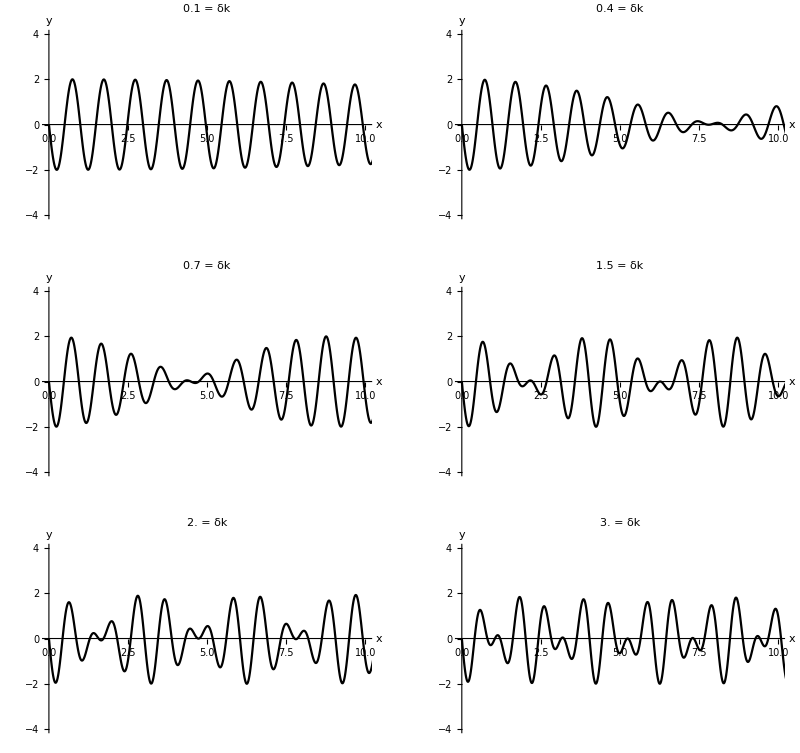

Looks reasonable because greater δk = greater difference in frequencies between waves

(ii)

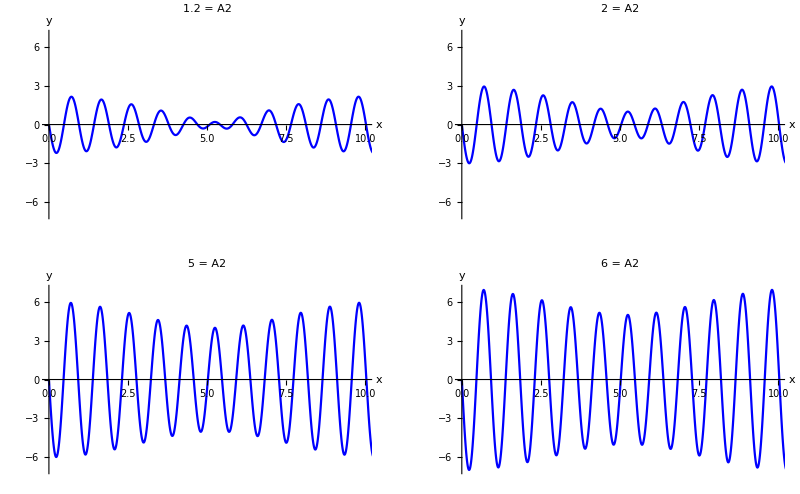

Changing amplitude changes size of resultant wave

iii)

Standing near x=10 I would hear noise that oscillates between louder and softer

```mathematica
(*2*)
Remove["Global`*"]

y1[A1_,x_,t_]:=A1*Sin[k1*(x-v*t)];
y2[A2_,x_,δk_,t_]:=A2*Sin[(k1+δk)*(x-v*t)];
yr[A1_,A2_,x_,δk_,t_]:=y1[A1,x,t]+y2[A2,x,δk,t];

v=1;
k1 = 2π;
tmax = 30;

pixr[A1_,A2_,δk_,t_]:=Plot[yr[A1,A2,0,δk,t],{t,0,tmax},PlotStyle->Black,PlotLabel->δk" = δk" ,AxesLabel->{"x","y"} ]
plot[A1_,A2_,δk_,t_]:=Show[pixr[A1,A2,δk,t],PlotRange->{{0,10},{-4,4}}]

δ1i=plot[1,1,0.1,t];
δ2i=plot[1,1,0.4,t];
δ3i=plot[1,1,0.7,t];
δ4i=plot[1,1,1.5,t];
δ5i=plot[1,1,2.0,t];
δ6i=plot[1,1,3.0,t];

Print["2)(i)"];
GraphicsGrid[{{δ1i,δ2i},{δ3i,δ4i},{δ5i,δ6i}}]
Print["Looks reasonable because greater δk = greater difference in frequencies between waves"]

pixr2[A1_,A2_,δk_,t_]:=Plot[yr[A1,A2,0,δk,t],{t,0,tmax},PlotStyle->Blue,PlotLabel->A2" = A2" ,AxesLabel->{"x","y"} ]
plot2[A1_,A2_,δk_,t_]:=Show[pixr2[A1,A2,δk,t],PlotRange->{{0,10},{-7,7}}]

δ1ii=plot2[1,1.2,0.6,t];
δ2ii=plot2[1,2,0.6,t];
δ3ii=plot2[1,5,0.6,t];
δ4ii=plot2[1,6,0.6,t];

Print["(ii)"]
GraphicsGrid[{{δ1ii,δ2ii},{δ3ii,δ4ii}}]
Print["Changing amplitude changes size of resultant wave"];

pixr3[A1_,A2_,δk_,t_]:=Plot[yr[A1,A2,x,δk,t],{x,0,20},PlotStyle->Black,AxesLabel->{"x","y"} ]
plot3[A1_,A2_,δk_,t_]:=Show[pixr3[A1,A2,δk,t],PlotRange->{{0,20},{-4,4}}]

Print["iii)"]
Animate[plot3[1,2,0.5,t],{t,0,30}]
Print["Standing near x=10 I would hear noise that oscillates between louder and softer"]
```

3)(i)The wavefunction = ⅇ^(-ⅈ k0 x+ⅈ t ω0)

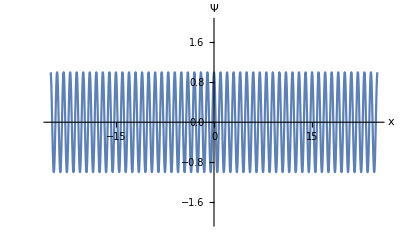

(ii)The wavefunction = (2 ⅇ^(-ⅈ k0 x+ⅈ t ω0) Sin[1/2 δk (x-t ω0p)])/(x-t ω0p)

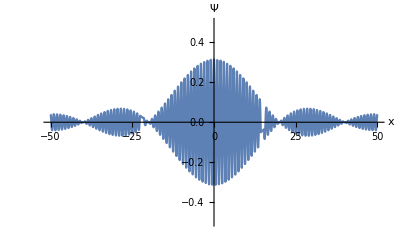

(iii)The wavefunction = -(ⅈ √2 ⅇ^(-1/2 ⅈ (2 k0 x+x δk-2 t ω0+t δk ω0p)) δk (ⅇ^(ⅈ x δk) (ⅈ π-2 x δk+2 t δk ω0p)+ⅇ^(ⅈ t δk ω0p) (ⅈ π+2 δk (x-t ω0p))))/((π-2 x δk+2 t δk ω0p) (π+2 δk (x-t ω0p)))

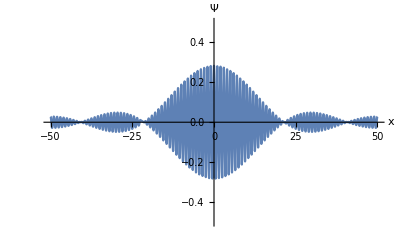

(iv)The wavefunction = (ⅇ^(-1/2 ⅈ (2 k0 x+x δk-2 t ω0+t δk ω0p)) (ⅈ ⅇ^(ⅈ x δk) (2 ⅈ-x δk+t δk ω0p)+ⅇ^(ⅈ t δk ω0p) (2+3 ⅈ δk (x-t ω0p))))/(4 δk (x-t ω0p)^2)

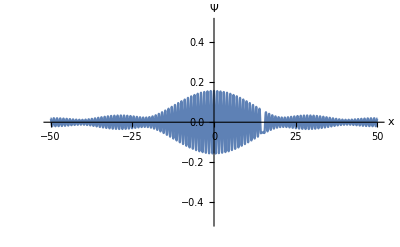

(v)The wavefunction = -1/8 ⅇ^(-ⅈ k0 x+ⅈ t ω0) δk (ExpIntegralE[-2,-1/2 ⅈ δk (x-t ω0p)]+ExpIntegralE[-2,1/2 ⅈ δk (x-t ω0p)])

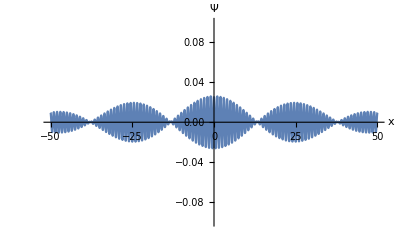

Superimposing waves with similar frequencies results in beats

```mathematica
(*3*)
Remove["Global`*"]
SetAttributes[{k0,ω0,ω0p,δk},Constant];
$Assumptions = {Element[{k0,ω0,ω0p,δk,t},Reals] && k0>0 && ω0>0 && δk>0};

clear:=Clear[k0,δk,ω0,ω0p]
clist:={
k0 = 2 π,
δk =  0.1 π,
ω0 = 0.2 π,
ω0p = 0.3 π
} 

klo = k0 - δk/2;
khi = k0 + δk/2;
ω=ω0+ω0p*(k-k0);

Ai[k_]=DiracDelta[k-k0];
Aii[k_]=1;
Aiii[k_]=Cos[π/(2*δk)*(k-k0)];
Aiv[k_]= (k-k0+δk)/(2*δk);
Av[k_]=(k-k0)^2/(δk)^2;

Aih=HoldForm[DiracDelta[k-k0]];
Aiih=HoldForm[1];
Aiiih=HoldForm[Cos[π/(2*δk)*(k-k0)]];
Aivh= HoldForm[(k-k0+δk)/(2*δk)];Avh=HoldForm[(k-k0)^2/(δk)^2];

SuperStar[z_]:=Conjugate[z];
Ψi[x_,t_]=Integrate[Ai[k]*E^(I*(ω*t-k*x)),{k,klo,khi}]//Simplify;
Print["3)(i)The wavefunction = ", Ψi[x,t]]

clist;
Ai[x_,t_]=1/2(Ψi[x,t]+SuperStar[Ψi[x,t]]);
xr = 25;
yr = 2;
r = {{-xr,xr},{-yr,yr}};
ploti=Plot[Ai[x,0],{x,-xr,xr},PlotRange->r,AxesLabel->{x,Ψ}]


clear
Ψii[x_,t_]=Integrate[Aii[k]*E^(I*(ω*t-k*x)),{k,klo,khi}]//Simplify;
Print["(ii)The wavefunction = ", Ψii[x,t]]

clist;
Aii[x_,t_]=1/2(Ψii[x,t]+SuperStar[Ψii[x,t]]);
xr = 50;
yr = 0.5;
r = {{-xr,xr},{-yr,yr}};
plot2=Plot[Aii[x,0],{x,-xr,xr},PlotRange->r,AxesLabel->{x,Ψ}]


clear
Ψiii[x_,t_]=Integrate[Aiii[k]*E^(I*(ω*t-k*x)),{k,klo,khi}]//Simplify;
Print["(iii)The wavefunction = ", Ψiii[x,t]]

clist;
Aiii[x_,t_]=1/2(Ψiii[x,t]+SuperStar[Ψiii[x,t]]);
xr = 50;
yr = 0.5;
r = {{-xr,xr},{-yr,yr}};
plotiii=Plot[Aiii[x,0],{x,-xr,xr},PlotRange->r,AxesLabel->{x,Ψ}]


clear
Ψiv[x_,t_]=Integrate[Aiv[k]*E^(I*(ω*t-k*x)),{k,klo,khi}]//Simplify;
Print["(iv)The wavefunction = ", Ψiv[x,t]]

clist;
Aiv[x_,t_]=1/2(Ψiv[x,t]+SuperStar[Ψiv[x,t]]);
xr = 50;
yr = 0.5;
r = {{-xr,xr},{-yr,yr}};
plotiv=Plot[Aiv[x,0],{x,-xr,xr},PlotRange->r,AxesLabel->{x,Ψ}]


clear
Ψv[x_,t_]=Integrate[Av[k]*E^(I*(ω*t-k*x)),{k,klo,khi}]//Simplify;
Print["(v)The wavefunction = ", Ψv[x,t]]

clist;
Av[x_,t_]=1/2(Ψv[x,t]+SuperStar[Ψv[x,t]]);
xr = 50;
yr = 0.1;
r = {{-xr,xr},{-yr,yr}};
plotv=Plot[Av[x,0],{x,-xr,xr},PlotRange->r,AxesLabel->{x,Ψ}]

Print["Superimposing waves with similar frequencies results in beats"]
```

```mathematica
(*4*)
Remove["Global`*"]
SetAttributes[{h,f,L},Constant];
$Assumptions = {Element[{h,f,L,x},Reals]&& Element[n,Integers]&& h>0  && 0≤f≤1 && L>0 && 0≤x≤L };

np = 2;
f[1][x_]=h*x/(f*L);
x1[1]=0;
x2[1]=f*L;
f[2][x_]=h-h*(x-f*L)/(L-f*L);
x1[2]=x2[1];
x2[2]=L;

b[n_]=2/L*Sum[Integrate[f[i][x]*Sin[n*π*x/L],{x,x1[i],x2[i]}],{i,1,np}]//Refine//Simplify;
L =10;
f=1/3;
h=2;
vx = 1;
nterms = 50;
xmn = x1[1];
xmx = x2[np];
yr = 5;
r = {{xmn,xmx},{-yr,yr}};

blist = Table[{n,b[n]},{n,1,nterms}];

Print["4)The displacement for plucked string = ",
dp1[x_,t_]=Sum[b[n]*Sin[n*π*x/L]*Cos[n*π*vx*t/L],{n,1,5}]," + ..."]

dp[x_,t_]=Sum[b[n]*Sin[n*π*x/L]*Cos[n*π*vx*t/L],{n,1,nterms}];

(*Plot!*)
animePlot[t_]:=Plot[dp[x,t],{x,xmn,xmx},PlotRange->r,AxesLabel->{x,"f(x)"}]

Print["Visually, the wave looks like"]
Animate[animePlot[t],{t,0,50,0.2},DisplayAllSteps->True]
Print["Since initial displacement = L/3, no harmonics with nodes which points at L/3 are excited"]
```

4)The displacement for plucked string = (9 √3 Cos[(π t)/10] Sin[(π x)/10])/π^2+(9 √3 Cos[(π t)/5] Sin[(π x)/5])/(4 π^2)-(9 √3 Cos[(2 π t)/5] Sin[(2 π x)/5])/(16 π^2)-(9 √3 Cos[(π t)/2] Sin[(π x)/2])/(25 π^2) + ...

Visually, the wave looks like

Since initial displacement = L/3, no harmonics with nodes which points at L/3 are excited

```mathematica
(*5*)
Remove["Global`*"]
SetAttributes[{n,α,b},Constant];
$Assumptions={Element[{n,α,x,b},Reals]&&b>0&&N>0&&α>0&&x≥0};

n=4;
f[α_,x_]:=n*E^(-α*x^2);
F[α_,k_]=1/Sqrt[2π]*Integrate[f[α,x]*E^(-I*k*x),{x,-∞,∞}];

r = {{-5,5},{0,5}};
rt = {{-5,5},{0,15}};
plotG[α_,x_] :=Plot[f[α,x],{x,-20,20},PlotRange->r,PlotLabel->"f(x) = Ne^(-α SuperscriptBox[x, 2])",AxesLabel->{x,f[x]},ImageSize->Medium]
plotT[α_,k_]:=Plot[F[α,k],{k,-20,20},PlotRange->rt,PlotLabel->"Fourier Transform",AxesLabel->{k,F[k]},ImageSize->Medium]

Print["5a)"]
Manipulate[{plotG[α,x],plotT[α,k]},{α,0.05,30}]
Print["As Gaussian's width decreases transform's width increases."]
```

5a)

As Gaussian's width decreases transform's width increases.

```mathematica
(***5b***)
Remove["Global`*"]
SetAttributes[a,Constant];
$Assumptions=Element[{x,a},Reals];

f[a_,x_]=Piecewise[{{0,x<-a},{1,-a≤ x≤ a},{0,x>a}}];
F[a_,k_]=1/Sqrt[2*π]*Integrate[f[a,x]*E^(-I*k*x),{x,-∞,∞}];

plot[a_]:=Plot[f[a,x],{x,-20,20},PlotRange->{{-a-5,a+5},{-2,2}},PlotLabel->"Box Function",AxesLabel->{x,"f(x)"},ImageSize->Medium]
transPlot[a_]:=Plot[F[a,k],{k,-20,20},PlotRange->{{-a,a},{-2,20}},PlotLabel->"Fourier Transform",AxesLabel->{k,"F(k)"},ImageSize->Medium]

Print["5b)"]
Manipulate[{plot[a],transPlot[a]},{a,1,20}]
Print["larger a = less precision for position, more precision for momentum"]
```

5b)

larger a = less precision for position, more precision for momentum

```mathematica
(*6*)
Remove["Global`*"]

SetAttributes[{ω0,ω},Constant]
$Assumptions=Element[{ω0,ω},Reals];
yi[t_]=Sin[ω0*t]//TrigToExp;
Fi[ω_]=FourierTransform[yi[t],t,ω];
Print["6)(i)Spectral decomposition = ", Fi[ω]]

SetAttributes[{ω1,ω2},Constant]
yi2[t_]=Sin[ω1*t]*Sin[ω2*t];
Fi2[ω_]=FourierTransform[yi2[t],t,ω];
Print["(ii)Spectral decomposition = ", Fi2[ω]]

SetAttributes[{k0,δk},Constant];
$Assumptions=Element[{k0,δk},Reals];
Ψiii[x_]=-1/8 ⅇ^(-ⅈ k0 x) δk (ExpIntegralE[-2,-1/2 ⅈ x δk]+ExpIntegralE[-2,(ⅈ x δk)/2]);
(* takes too long to run
Fi3[k_]=FourierTransform[Ψiii[x],x,k];
Print["\n(iii)\nThe spectral decomposition of Ψ(t) = ", Fi3[k]]
*)
```

6)(i)Spectral decomposition = ⅈ √(π/2) DiracDelta[ω-ω0]-ⅈ √(π/2) DiracDelta[ω+ω0]

(ii)Spectral decomposition = -1/2 √(π/2) DiracDelta[ω-ω1-ω2]+1/2 √(π/2) DiracDelta[ω+ω1-ω2]+1/2 √(π/2) DiracDelta[ω-ω1+ω2]-1/2 √(π/2) DiracDelta[ω+ω1+ω2]